```mathematica
I1[phiBar_?NumericQ,kappa_?NumericQ]:=NIntegrate[√(Ebar+1)(1+Ebar phiBar/(kappa-3/2))^(-(kappa+1)),{Ebar,0,∞}]
```

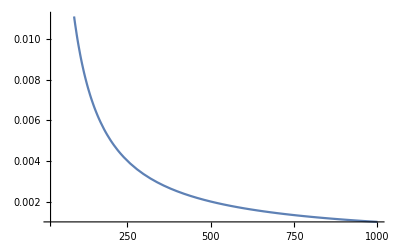

```mathematica
Plot[I1[phiBar,10000],{phiBar,20,1000}]
```

## Looking at 20180206-Verify_eq_5a_in_Liemohn_and_Khazanov[...].pdf

#### Integ 1, which needs to be multiplied by Cp6 (e (ΔΦ))^(3/2)

```mathematica
Limit[(1+Ebar phiBar/(kappa-3/2))^(-(kappa+1)),kappa->∞]
```

ⅇ^(-Ebar phiBar)

```mathematica
Integ1MaxwellLimit=Cp6AndEdeltaPhiThing*Integrate[√(Ebar+1)Exp[-Ebar phiBar],{Ebar,0,∞},Assumptions->phiBar≥ 1]
```

Cp6AndEdeltaPhiThing (1/phiBar+(ⅇ^phiBar √π Erfc[√phiBar])/(2 phiBar^(3/2)))

```mathematica
Integ1=Cp6AndEdeltaPhiThing*Integrate[√(Ebar+1)(1+Ebar phiBar/(kappa-3/2))^(-(kappa+1)),{Ebar,0,∞},Assumptions->phiBar≥ 1&&kappa>3/2]
```

1/(2 phiBar^(3/2))Cp6AndEdeltaPhiThing (-3+2 kappa) ((2^(1/2-2 kappa) (-3+2 kappa)^kappa (3-2 kappa+2 phiBar)^(1/2-kappa) Gamma[1-kappa] Gamma[-1+2 kappa])/Gamma[1+kappa]+(√phiBar Hypergeometric2F1[-1/2,1,1-kappa,(-3+2 kappa)/(2 phiBar)])/kappa)

```mathematica
Limit[(-3+2 kappa) (2^(1/2-2 kappa) (-3+2 kappa)^kappa (3-2 kappa+2 phiBar)^(1/2-kappa) Gamma[1-kappa] Gamma[-1+2 kappa])/Gamma[1+kappa],kappa->∞]
```

-(2 ⅇ^phiBar √π)/(-1+ⅇ^(2 ⅈ Interval[{0,π}]))

```mathematica
Limit[Hypergeometric2F1[-1/2,1,1-kappa,(-3+2 kappa)/(2 phiBar)],kappa->∞,Direction->Reals]
```

lim_(kappa→_ℝ∞) Hypergeometric2F1[-1/2,1,1-kappa,(-3+2 kappa)/(2 phiBar)]

#### Integ 2, which needs to be multiplied by -(Cp6 (e (ΔΦ))^(3/2))/(R_B-1). THEN nFac wil be I1 + I2

```mathematica
Limit[(1+EbarStar phiBarOverRBMinus1/(kappa - 3/2))^(-(kappa+1)),kappa->∞]
```

ⅇ^(-EbarStar phiBarOverRBMinus1)

```mathematica
Integ2MaxwellLimit=-Cp6AndEdeltaPhiThing/(RB-1)Integrate[√(1-EbarStar)Exp[-EbarStar phiBarOverRBMinus1],{EbarStar,0,1},Assumptions->phiBarOverRBMinus1>0]
```

-(Cp6AndEdeltaPhiThing (1/phiBarOverRBMinus1-DawsonF[√phiBarOverRBMinus1]/phiBarOverRBMinus1^(3/2)))/(-1+RB)

#### Totalt

```mathematica
totalt=Integ1MaxwellLimit+Integ2MaxwellLimit/.phiBarOverRBMinus1->phiBar/(RB-1)
```

-(Cp6AndEdeltaPhiThing ((-1+RB)/phiBar-DawsonF[√(phiBar/(-1+RB))]/(phiBar/(-1+RB))^(3/2)))/(-1+RB)+Cp6AndEdeltaPhiThing (1/phiBar+(ⅇ^phiBar √π Erfc[√phiBar])/(2 phiBar^(3/2)))

```mathematica
Simplify[totalt]
```

(Cp6AndEdeltaPhiThing (2 √phiBar DawsonF[√(phiBar/(-1+RB))]+ⅇ^phiBar √π √(phiBar/(-1+RB)) Erfc[√phiBar]))/(2 phiBar^(3/2) √(phiBar/(-1+RB)))

This works out to be n/n_0=1/2 e^(ϕ̄)erfc[√(ϕ̄)] +((R_B-1)/π)^(1/2)DawsonF[√((ϕ̄)/(R_B-1))], which is just what we want!!!

#### Bro

```mathematica
Integrate[v^2(1-v^2/κ0)^κ0,v]
```

1/3 v^3 Hypergeometric2F1[3/2,-κ0,5/2,v^2/κ0]

```mathematica
Hypergeometric2F1[3/2,-k,5/2,0]
```

1

```mathematica
Limit[Hypergeometric2F1[3/2,-k,5/2,a],a->0,Direction->"FromBelow"]
```

1

```mathematica
Limit[Hypergeometric2F1[3/2,-k,5/2,a],a->0,Direction->"FromAbove"]
```

1

```mathematica
Limit[Hypergeometric2F1[3/2,-k,5/2,a],a->0,Direction->Complexes]
```

1

```mathematica
Limit[Hypergeometric2F1[3/2,-k,5/2,a],a->0,Direction->Reals]
```

1

```mathematica
Manipulate[Plot[{1/phiBar,
```